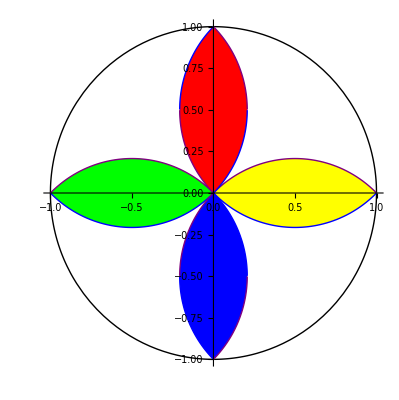

```mathematica
a=1;
f0[x_]=√(a^2 - x^2);
f0D[x_]=-√(a^2 - x^2);
f1[x_]=a/2-Sqrt[(a)^2/2-(x-a/2)^2];
f2[x_]=a/2+Sqrt[(a)^2/2-(x-a/2)^2];
f3[x_]=a/2+Sqrt[(a)^2/2-(x+a/2)^2];
f4[x_]=a/2-Sqrt[(a)^2/2-(x+a/2)^2];


p0=Plot[{f0[x],f0D[x]},{x,-1,1},PlotStyle->{{Thick,Black}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic];


g1[x_]=-a/2+Sqrt[(a)^2/2-(x-a/2)^2];
g2[x_]=-a/2-Sqrt[(a)^2/2-(x-a/2)^2];
g3[x_]=-a/2-Sqrt[(a)^2/2-(x+a/2)^2];
g4[x_]=-a/2+Sqrt[(a)^2/2-(x+a/2)^2];
pright=Plot[{g1[x],f1[x]},{x,0,1},PlotStyle->{{Thick,Purple},{Thick,Blue}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,Filling->{1->{2}},FillingStyle->Yellow];

pUpL=Plot[{f1[x],f2[x]},{x,-0.5,0},PlotStyle->{{Thick,Purple},{Thick,Blue}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,Filling->{1->{2}},FillingStyle->Red,PlotRange->All];
pUpR=Plot[{f3[x],f4[x]},{x,0,0.5},PlotStyle->{{Thick,Purple},{Thick,Blue}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,Filling->{1->{2}},FillingStyle->Red,PlotRange->All];
pleft=Plot[{g4[x],f4[x]},{x,-1,0},PlotStyle->{{Thick,Purple},{Thick,Blue}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,Filling->{1->{2}},FillingStyle->Green];
pDnR=Plot[{g3[x],g4[x]},{x,0,0.5},PlotStyle->{{Thick,Purple},{Thick,Blue}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,Filling->{1->{2}},FillingStyle->Blue,PlotRange->All];
pDnL=Plot[{g1[x],g2[x]},{x,-0.5,0},PlotStyle->{{Thick,Purple},{Thick,Blue}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic,Filling->{1->{2}},FillingStyle->Blue,PlotRange->All];
p1=Plot[{g1[x],g2[x],g3[x],g4[x]},{x,-1,0.5},PlotStyle->{{Thick,Black},{Thick,Red},{Thick,Green},{Thick,Purple}},Axes->True,AxesOrigin->{0,0},AspectRatio->Automatic];
Show[p0,pright,pleft,pUpR,pUpL,pDnR,pDnL,PlotRange->{-1,1}]
```

# Area of a triangle within a polygon

```mathematica
ClearAll["Global`*"];
```

```mathematica
Manipulate[
Column[{
Item[
Which[answer&&n==4,Column[{Style["\nArea of shaded triangle = k^2/24",16, Black],
Style["Area of Square = k^2\n",16, Black]}],answer&&n==6,
Column[{Style["\nArea of shaded triangle = (√3)/15",16, Black],Style["Area of Hexagon = (3 SqrtBox[3] SuperscriptBox[k, 2])/2\n",16, Black]}],
answer&&n==8,Column[{Style["\nArea of shaded triangle = (√2)/8",16, Black],Style["Area of Octagon = 2 (1 + √2) k^2\n",16, Black]}],True,Style["\nCalculate the area of the yellow triangle\ngiven that the length of the figure's side is k\n",16,Black]],Alignment->Left,Frame->True],
Item[
α8=ArcTan[(Cos[π/8] Sin[π/4] - Sin[13π/8])/Cos[13π/8]];
θ= ArcTan[(Tan[π/6]-Sin[5π/3])/Cos[5π/3]];
Graphics[{Circle[],{PointSize[0.02],Blue,Point[{0,0}]},
Which[n==4,{{Thick,Line[Table[{Cos[t],Sin[t]},{t,π/n,2π+π/n,2π/n}]]},
Line[{{Cos[(n-1)π/n],0},{Cos[π/n],0}}],Line[{{Cos[(n-1)π/n],0},{Cos[π/n],Sin[π/4]}}],Line[{{Cos[(n-1)π/n],Sin[(n-1)π/n]},{Cos[π/n],0}}],
Line[{{Cos[(n+1)π/n],Sin[(n+1)π/n]},{0,Sin[π/n]/(n-2)}}],Line[{{Cos[(2 n-1)π/n],Sin[(2 n-1)π/n]},{0,Sin[π/n]/2}}],{EdgeForm[{Thick,Red}],FaceForm[Yellow],Polygon[{{0,Sin[π/n]/(n-2)},{-Cos[π/n]/(n-1),0},{Cos[π/n]/(n-1),0}}]}
},n==6,
{{Thick,Line[Table[{Cos[2π k/n],Sin[2π k/n]},{k,0,n}]]},Point[{0,Tan[π/6]}],Line[{{Cos[0],0},{Cos[ π],0}}],{Black,Line[{{Cos[0],0},{Cos[4π/n],Sin[4π/n]}}],Line[{{Cos[π],0},{Cos[2π/n],Sin[2π/n]}}],Line[{{Cos[10π/( n)],Sin[10 π/n]},{0,Tan[π/n]}}],Line[{{Cos[8 π/n],Sin[8 π/n]},{0,Tan[π/n]}}]},{EdgeForm[{Thick,Red}],FaceForm[Yellow],Polygon[{{0,Tan[π/n]},{Tan[π/n]/Tan[θ],0},{-Tan[π/n]/Tan[θ],0}}]
}

},
n==8,
{{Thick,Line[Table[{Sin[t],Cos[t]},{t,π/8,2 π+π/8,2 π/8}]],Blue,Circle[],PointSize[0.02],Point[{0,0}],Point[{Cos[π/8],0}],Point[{Cos[7π/8],0}],Line[{{Cos[7π/8],0},{Cos[π/8],0}}]},{Black,Line[{{Cos[7π/8],0},{Cos[3π/8],Sin[3π/8]}}],Line[{{Cos[π/8],0},{Cos[5π/8],Sin[5π/8]}}],Line[{{Cos[11π/8],Sin[11π/8]},{0,Cos[π/8]Sin[π/4]}}],Line[{{Cos[13π/8],Sin[13π/8]},{0,Cos[π/8]Sin[π/4]}}]},{EdgeForm[{Thick,Red}],FaceForm[Yellow],Polygon[{{0,Cos[π/8]Sin[π/4]},{Cos[π/8]Sin[π/4]/Tan[α8],0},{-Cos[π/8]Sin[π/4]/Tan[α8],0}}]}
},

Mod[n,11]==0 ||Mod[n,9]==0 ||Mod[n,7]==0,{Thick,Line[Table[{Cos[2π k/n],Sin[2π k/n]},{k,n/4,(n+n/4)}]]},
Mod[n,10]==0,{Thick,Line[Table[{Cos[t],Sin[t]},{t,4π/n,2π+4π/n,2π/(n)}]]},
Mod[n,5]==0,{Thick,Line[Table[{Cos[t],Sin[t]},{t,π/(2n),2π+2π/(n),2π/(n)}]]},
True,{{Thick,Line[Table[{Cos[2π k/n],Sin[2π k/n]},{k,0,n}]]},Point[{0,Tan[π/6]}],Line[{{Cos[0],0},{Cos[ π],0}}]

}]},ImageSize->400],Alignment->{Center},Frame->True]
}],
Row[{
Control[{{n,6,"# Vertices"},4,8,2,Appearance->"Labeled",ImageSize->Tiny}],Spacer[30],Control[{{answer,False,"answer"},{False,True}}]}],TrackedSymbols:>{n,answer}]
```